## Import Data From NetCDF

```mathematica
SetDirectory["/Users/penn/Documents/Code/Github/PhDThesis/data/SST"];
```

```mathematica
Import["sst.mnmean.nc"]
```

{lat,lon,sst,time,time_bnds}

```mathematica
data = Import["sst.mnmean.nc", {"Datasets", "sst"}];
```

```mathematica
Dimensions[data]
```

{415,180,360}

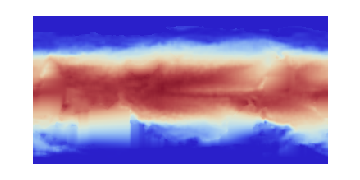

```mathematica
ArrayPlot[Reverse@data[[1,;;,;;]],ColorFunction->"ThermometerColors",ImageSize->Medium]
```